```mathematica
(* integral for Ray *) 
delta=0.35; (*merging distance *)
f[v_]=(v^5*(v+1)^4*(v^2+1)^5)^(-1/3);
fSeries0[v_]=(Series[f[v],{v,0,10}])*HeavisideTheta[v,1-v-delta]//Normal ;
fSeries1[v_]=(Series[f[v],{v,1,5}]//Normal )*HeavisideTheta[v+delta-1,1.5-v-delta];
fSeries15[v_]=(Series[f[v],{v,1.5,5}]//Normal )*HeavisideTheta[v+delta-1.5,2-v-delta];
fSeries2[v_]=(Series[f[v],{v,2,5}]//Normal) *HeavisideTheta[v+delta-2,2.5-v-delta];
fSeries25[v_]=(Series[f[v],{v,2.5,5}]//Normal )*HeavisideTheta[v+delta-2.5,3-v-delta];
fSeries3[v_]=(Series[f[v],{v,3,5}]//Normal )*HeavisideTheta[v+delta-3,3.5-v-delta];
fSeries35[v_]=(Series[f[v],{v,3.5,5}]//Normal )*HeavisideTheta[v+delta-3.5,4-v-delta];
fSeries4[v_]=(Series[f[v],{v,4,5}]//Normal) *HeavisideTheta[v+delta-4,4.5-v-delta];
fSeries45[v_]=(Series[f[v],{v,4.5,5}]//Normal )*HeavisideTheta[v+delta-4.5,5-v-delta];
fSeries5[v_]=((v+0.24955)^(-19/3))*HeavisideTheta[v+delta-5]//Normal ;
fApprox[v_]=fSeries0[v]+fSeries1[v]+fSeries15[v]+fSeries2[v]+fSeries25[v]+fSeries3[v]+fSeries35[v]+fSeries4[v]+fSeries45[v]+fSeries5[v];
```

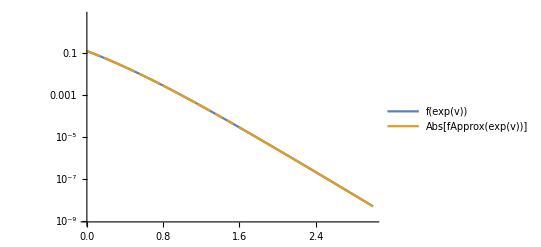

```mathematica
LogPlot[{f[Exp[v]],Abs[fApprox[Exp[v]]]},{v,0,3},PlotLegends->"Expressions"]
```

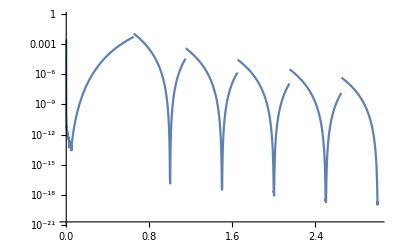

```mathematica
LogPlot[{Abs[f[v]-fApprox[v]]},{v,0,3},PlotLegends->"Expressions"]
```

```mathematica
NIntegrate[f[v]-fApprox[v],{v,0,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`v near TraditionalForm`{v} = TraditionalForm`{0.654219}. NIntegrate obtained TraditionalForm`0.0008719055535950042` and TraditionalForm`7.683963982842273`*^-6 for the integral and error estimates.

0.000871906

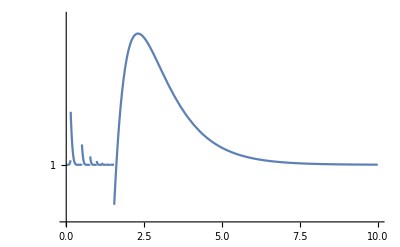

```mathematica
LogPlot[f[Exp[v]]/fApprox[Exp[v]],{v,0,10},PlotLegends->"Expressions"]
```

```mathematica
Integrate[fApprox[v],{v,τ^4,1/(τ^4)},Assumptions->0.0001<τ<0.5]
```

(τ^20 (0.0000390992-193.737/((0.24955+1./τ^4)^(1/3)))+0.000783395 τ^16+0.00627846 τ^12+0.0251591 τ^8+0.050409 τ^4+0.0403999)/((1. τ^4+4.00721)^5)+1/τ^(8/3)(-5.39358 τ^(8/3)-0.122366 τ^44+0.0462639 τ^40+0.320848 τ^36-0.257952 τ^32-0.142212 τ^28+0.0509545 τ^24+0.479899 τ^20-0.450617 τ^16-0.21164 τ^12+0.0833333 τ^8+4. τ^4+1.5)+0.137031

```mathematica
soln=%
soln//StandardForm
```

(τ^20 (0.0000390992-193.737/((0.24955+1./τ^4)^(1/3)))+0.000783395 τ^16+0.00627846 τ^12+0.0251591 τ^8+0.050409 τ^4+0.0403999)/((1. τ^4+4.00721)^5)+1/τ^(8/3)(-5.39358 τ^(8/3)-0.122366 τ^44+0.0462639 τ^40+0.320848 τ^36-0.257952 τ^32-0.142212 τ^28+0.0509545 τ^24+0.479899 τ^20-0.450617 τ^16-0.21164 τ^12+0.0833333 τ^8+4. τ^4+1.5)+0.137031

0.137031+1/((4.00721+1. τ^4)^5)(0.0403999+0.050409 τ^4+0.0251591 τ^8+0.00627846 τ^12+0.000783395 τ^16+(0.0000390992-193.737/((0.24955+1./τ^4)^(1/3))) τ^20)+1/τ^(8/3)(1.5-5.39358 τ^(8/3)+4. τ^4+0.0833333 τ^8-0.21164 τ^12-0.450617 τ^16+0.479899 τ^20+0.0509545 τ^24-0.142212 τ^28-0.257952 τ^32+0.320848 τ^36+0.0462639 τ^40-0.122366 τ^44)

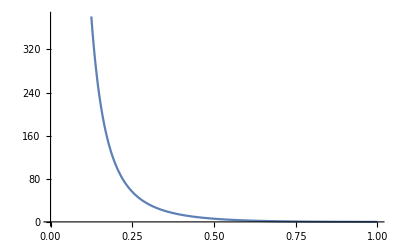

```mathematica
Plot[soln,{τ,0,1}]
```

```mathematica
data=Table[{i/100,soln/.τ->i/100},{i,100}];
logFunc[x_]=Fit[data,{1/x^3,1/x^2,1/x,1,x,x^2,x^3,Log[x],Log[x]^2,Log[x]^3,x Log[x],x Log[x]^2,x Log[x]^3,x^2Log[x]^2,x^2Log[x]^3},x]
```

-246298. x^3+0.128486/x^3+1.98921×10^7 x^2+48.0528/x^2+423920. x^2 log^3(x)-1.86634×10^6 x^2 log^2(x)+6.91368×10^7 x-19267.1/x-3.64821×10^6 x log^3(x)-332271. log^3(x)+6.63959×10^6 x log^2(x)-5.42638×10^6 log^2(x)-7.25816×10^7 x log(x)-3.56197×10^7 log(x)-8.87633×10^7

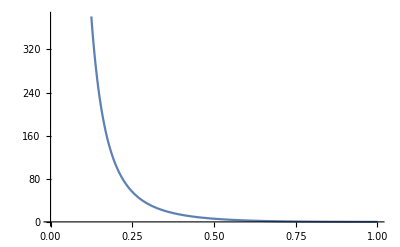

```mathematica
Plot[logFunc[t],{t,0,1}]
```